(1+2 Cos[x]+2 ⅈ Sin[x])/(1-2 Cos[x]-2 ⅈ Sin[x])

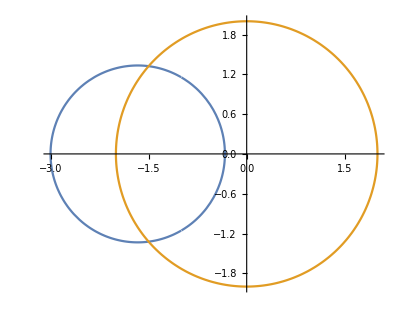

```mathematica
z[x_]:=2(Cos[x]+I*Sin[x])
g[x_]:=z[x]
F[z_]:=(z+1)/(-z+1)
t[x_]:=Nest[F,g[x],1]
t[x] //Simplify
grafico=ParametricPlot[{ReIm[t[x]],ReIm[z[x]]},{x,0,2Pi}];
Show[{grafico}]
```

```mathematica
(1+2 Cos[x]+2 ⅈ Sin[x])/(1-2 Cos[x]-2 ⅈ Sin[x])*(1-2 Cos[x]+2 ⅈ Sin[x])/(1-2 Cos[x]+2 ⅈ Sin[x])
```

(1+2 Cos[x]+2 ⅈ Sin[x])/(1-2 Cos[x]-2 ⅈ Sin[x])

```mathematica
(1+2 Cos[x]+2 ⅈ Sin[x])*(1-2 Cos[x]+2 ⅈ Sin[x])//FullSimplify
```

-3+4 ⅈ Sin[x]

```mathematica
(1-2 Cos[x]-2 ⅈ Sin[x])*(1-2 Cos[x]+2 ⅈ Sin[x])//FullSimplify
```

5-4 Cos[x]

```mathematica
(-3+4 ⅈ Sin[x])/(5-4 Cos[x])//FullSimplify
```

(-3+4 ⅈ Sin[x])/(5-4 Cos[x])

Comparamos la expresión (-3+4 ⅈ Sin[x])/(5-4 Cos[x]) con la circunferencia de centro -5/3 y radio 4/3.

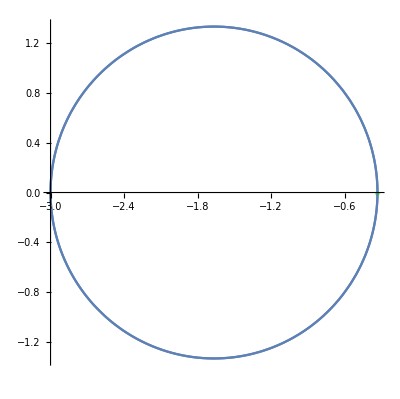

```mathematica
grafico=ParametricPlot[{ReIm[(-3+4 ⅈ Sin[x])/(5-4 Cos[x])]},{x,0,2Pi}];

graf=ParametricPlot[{ReIm[(1+1/3)(Cos[x]+I*Sin[x])-1-2/3]},{x,0,2Pi}];
punto=Graphics[{PointSize[Large],Green,Point[{-1/3,0}]}];
Show[{grafico,punto,graf}]
```

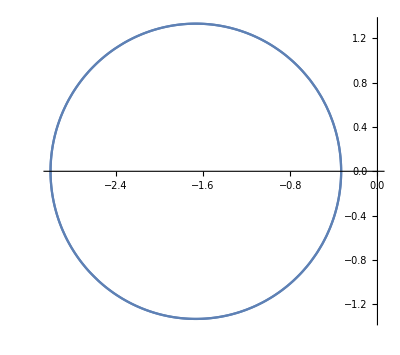

```mathematica
Show[graf,grafico]
```

la expresión (-3+4 ⅈ Sin[x])/(5-4 Cos[x]) de 0 a 2pi coincide con la circunferencia pero lleva una velocidad diferente.

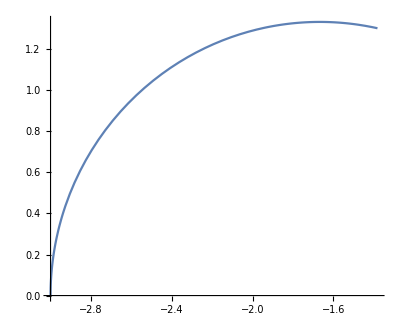

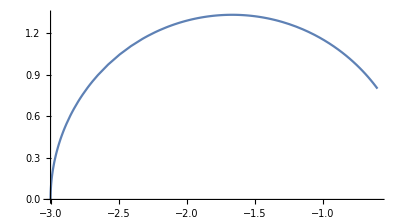

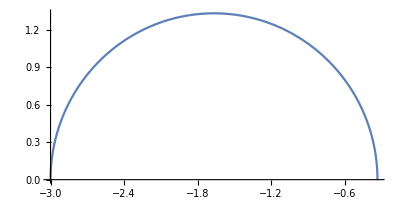

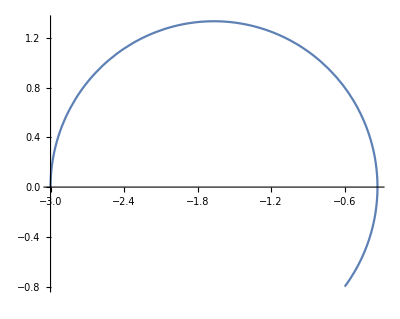

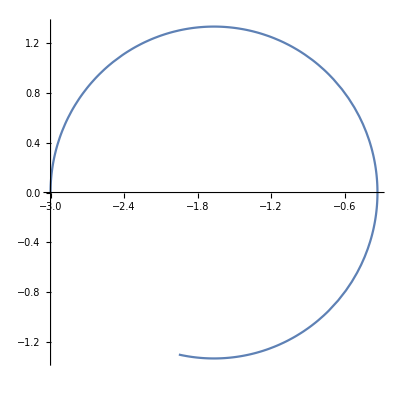

```mathematica
graf1=ParametricPlot[{ReIm[(-3+4 ⅈ Sin[x])/(5-4 Cos[x])]},{x,0,Pi/4}]
graf2=ParametricPlot[{ReIm[(-3+4 ⅈ Sin[x])/(5-4 Cos[x])]},{x,0,Pi/2}]
graf3=ParametricPlot[{ReIm[(-3+4 ⅈ Sin[x])/(5-4 Cos[x])]},{x,0,Pi}]
graf4=ParametricPlot[{ReIm[(-3+4 ⅈ Sin[x])/(5-4 Cos[x])]},{x,0,3*Pi/2}]
graf5=ParametricPlot[{ReIm[(-3+4 ⅈ Sin[x])/(5-4 Cos[x])]},{x,0,11*Pi/6}]
```